## Initialization

```mathematica
(* Switch to the directory the notebook and data files are in *)
SetDirectory[NotebookDirectory[]]
```

/Users/npadmana/myWork/np_sandbox/diff_transfer_fn

```mathematica
(* Number of files *)
```

```mathematica
nfiles = 5;
```

```mathematica
(* zvals -- hardcoded is not ideal, but why not?? *)
```

```mathematica
zvals= {0.04, 0.03, 0.02, 0.01, 0.00};
```

```mathematica
(* Set the file name list *)
```

```mathematica
fnames = "test_transfer_z"<>ToString[#]<>".dat"& /@ Range[0,nfiles-1];
```

```mathematica
(* Read in all the files *)
```

```mathematica
tData = Import[#, "Table"] & /@ fnames;
```

```mathematica
Dimensions[tData]
```

{5,692,7}

```mathematica
kval = tData[[1,All,1]];
```

```mathematica
transfers = tData[[All, All, {2,3}]];
```

```mathematica
Dimensions[transfers]
```

{5,692,2}

```mathematica
tDiff = transfers[[All,All,2]]- transfers[[All,All,1]];
```

```mathematica
Dimensions[tDiff]
```

{5,692}

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
qq = Thread[{kval, tDiff[[#,All]]}] & /@ Range[5];
```

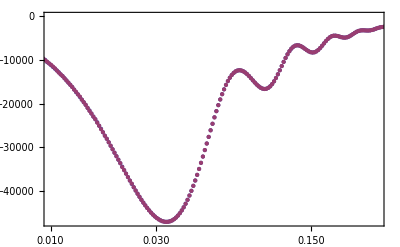

```mathematica
ListLogLinearPlot[qq[[{1,5}]], Frame->True, PlotRange->{{0.01,0.3}, Full}]
```

```mathematica
qq[[{1,5},Range[500,520]]]
```

{{{0.21875,-4777.},{0.223169,-4603.},{0.227678,-4353.},{0.232277,-4060.},{0.236969,-3767.},{0.241756,-3513.},{0.24664,-3325.},{0.251623,-3215.},{0.256706,-3180.},{0.261891,-3192.},{0.267182,-3220.},{0.272579,-3229.},{0.278086,-3194.},{0.283704,-3104.},{0.289435,-2968.},{0.295282,-2807.},{0.301247,-2650.},{0.307333,-2521.},{0.313541,-2434.},{0.319875,-2387.},{0.326337,-2364.}},{{0.21875,-4778.},{0.223169,-4604.},{0.227678,-4354.},{0.232277,-4061.},{0.236969,-3768.},{0.241756,-3513.},{0.24664,-3325.},{0.251623,-3216.},{0.256706,-3181.},{0.261891,-3193.},{0.267182,-3221.},{0.272579,-3230.},{0.278086,-3195.},{0.283704,-3105.},{0.289435,-2969.},{0.295282,-2808.},{0.301247,-2650.},{0.307333,-2521.},{0.313541,-2435.},{0.319875,-2387.},{0.326337,-2364.}}}

```mathematica
qq1 = Thread[{kval, tDiff[[5,All]]-tDiff[[1,All]]}];
```

```mathematica
qq2 = Thread[{kval, tDiff[[5,All]]-tDiff[[3,All]]}];
qq3 = Thread[{kval, tDiff[[5,All]] - tDiff[[2,All]]}];
```

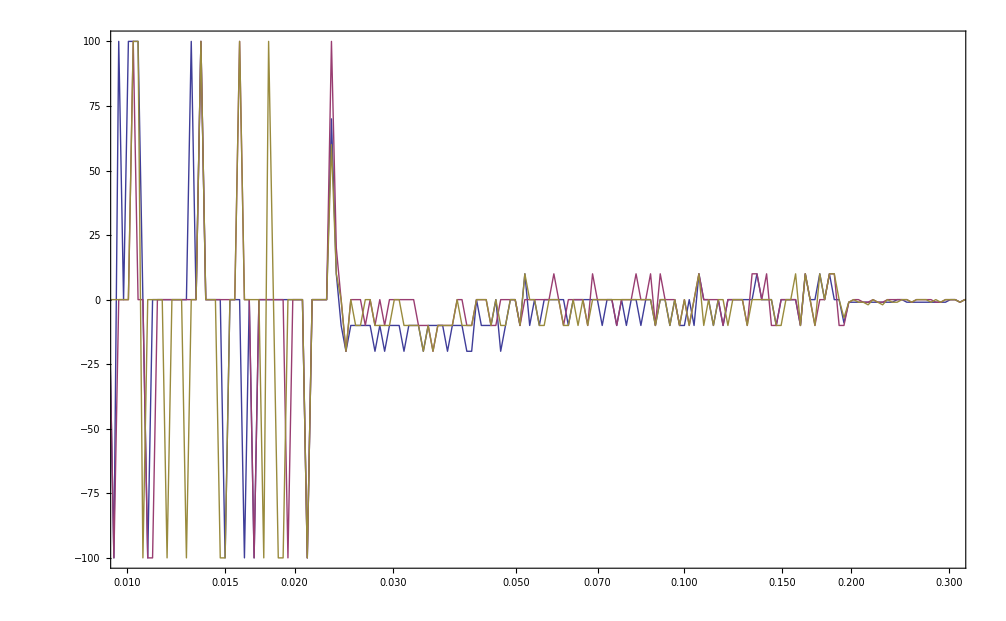

```mathematica
ListLogLinearPlot[{qq1,qq2,qq3}, Frame->True, PlotRange->{{0.01,0.3}, Full}, Joined->True]
```

```mathematica
norms = transfers[[All, 1, All]]
```

{{1.99711×10^7,1.99711×10^7},{2.00696×10^7,2.00696×10^7},{2.01684×10^7,2.01684×10^7},{2.02675×10^7,2.02675×10^7},{2.03668×10^7,2.03668×10^7}}

```mathematica
transfer1 = Transpose[ Transpose[transfers, {1,3,2}]/norms, {1,3,2}];
```

```mathematica
tDiff1 = transfer1[[All,All,2]]- transfer1[[All,All,1]];
```

```mathematica
zz = Thread[{kval, tDiff1[[#,All]]}] & /@ Range[5];
```

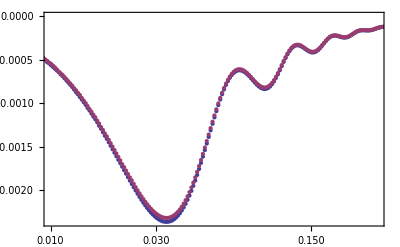

```mathematica
ListLogLinearPlot[zz[[{1,5}]], Frame->True, PlotRange->{{0.01,0.3}, Full}]
```

```mathematica
zz1 = Thread[{kval, tDiff1[[5,All]]-tDiff1[[1,All]]}];
```

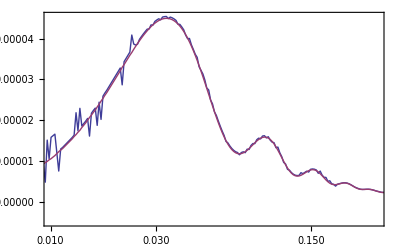

```mathematica
ListLogLinearPlot[{zz1, Transpose[Transpose[zz[[5]]]*{1,-0.485*0.04}]}, Frame->True, PlotRange->{{0.01,0.3}, Full}, Joined->True]
```

```mathematica
Dimensions[transfer1]
```

{5,692,2}

```mathematica
transfer1[[All, 1, All]]
```

{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}}